```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
ConfigureMaTeX["Ghostscript" -> FileNameJoin[{"C:","Program Files","gs","gs9.19","bin","gswin64c.exe"}]]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}",
" \\definecolor{spikeballred}{RGB}{216,43,43}"}]
```

C:\Users\Matthew\Documents\RbPapers\MBL\figures\cartoons\group_meeting_cartoons

{pdfLaTeX→C:\Program Files (x86)\MiKTeX 2.9\miktex\bin\pdflatex.exe,CacheSize→100,Ghostscript→C:\Program Files\gs\gs9.19\bin\gswin64c.exe}

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color,txfonts}, \definecolor{spikeballred}{RGB}{216,43,43}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
ColorData[93,"ColorList"]
ColorData[97,"ColorList"]
ColorData[98,"ColorList"]
ColorData[99,"ColorList"]
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧
atomgreen= RGBColor[0.8, 1,0.2];
atomgreen=ColorData[93,"ColorList"]⟦10⟧
```

{Hue[0, 0.8, 0.85],Hue[0.11, 0.75, 0.92],Hue[0.17, 0.6, 0.52],Hue[0.06, 0.75, 0.92],Hue[0.5, 0.5, 0.55],Hue[0.17, 0.67, 0.69],Hue[0.67, 0.33, 0.69],Hue[0.5, 0.33, 0.69],Hue[0.94, 0.5, 0.69],Hue[0.25, 0.6, 0.7]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.29, 0.588, 0.612],RGBColor[0.886243, 0.527215, 0.0910023],RGBColor[0.613966, 0.37652, 0.585084],RGBColor[0.521981, 0.66, 0.0942065],RGBColor[0.820916, 0.341417, 0.22514],RGBColor[0.436075, 0.482355, 0.72],RGBColor[0.915458, 0.67329, 0.0122632],RGBColor[0.687223, 0.3576, 0.441196],RGBColor[0.217839, 0.655694, 0.494605],RGBColor[0.868187, 0.436936, 0.13357],RGBColor[0.5170108648476139, 0.4061934810914317, 0.72],RGBColor[0.7591933320795998, 0.6647548146755111, 0.],RGBColor[0.7197093139665812, 0.342, 0.3604472092821826],RGBColor[0.28065605017210243, 0.5638751598623181, 0.6247872602065229],RGBColor[0.8683742223893867, 0.5222711119469331, 0.0853895995486561]}

{RGBColor[0.65, 0., 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.461492, 0.563303, 0.0104797],RGBColor[0.659814, 0.212037, 0.300311],RGBColor[0.212151, 0.39271, 0.8],RGBColor[0.784922, 0.524612, 0.0407096],RGBColor[0.515278, 0.224, 0.530342],RGBColor[0.111025, 0.56, 0.418696],RGBColor[0.6478640450004207, 0.3082039324993689, 0.019660112501051874],RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],RGBColor[0.7055434835026511, 0.5895048315002945, 0.],RGBColor[0.6531262919989895, 0.2133747416002021, 0.31145618000168407],RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]}

Hue[0, 0.8, 0.85]

Hue[0.25, 0.6, 0.7]

```mathematica
xlf={-2,-2,-2,-2};
xrf={-1.5,-0.5,0.5,2};
ycf={0,-1,-2,-3};
hf=0.3;

xl={-2,-2,-2,-2};
xr={-1.5,-0.5,0.5,2};
yc={0,-1,-2,-3};
h=0.4;

xnl={-2,-2,-2,-2};
xnr={-1.5,-0.5,-0.4,-0.35};
ync={0,-1,-2,-3};
hn=0.4;

tx=0.05;

FntSz=14;
```

## Particle Fluctuations

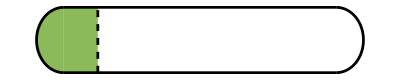

```mathematica
BackGrndBox1=Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.1],
{Rectangle[{xl⟦1⟧,yc⟦1⟧-h},{xnr⟦1⟧,yc⟦1⟧+h}]},
{Disk[{xl⟦1⟧,yc⟦1⟧},h,{π/2,3π/2}]},
{Disk[{xl⟦1⟧,yc⟦1⟧},h,{-π/2,π/2}]}
}];
OutLineBox1 = Graphics[{
RGBColor["Black"],
Thickness[0.005],{
Circle[{xl⟦1⟧,yc⟦1⟧},h,{π/2,3π/2}],
Circle[{xr⟦4⟧,yc⟦1⟧},h,{-π/2,π/2}],
Line[{{xl⟦1⟧,yc⟦1⟧-h},{xr⟦4⟧,yc⟦1⟧-h}}],
Line[{{xl⟦1⟧,yc⟦1⟧+h},{xr⟦4⟧,yc⟦1⟧+h}}]}
}];

Abreak1=Graphics[{
RGBColor["Black"],
Dashed,
Thickness[0.005],{
Line[{{xr⟦1⟧,yc⟦1⟧-h},{xr⟦1⟧,yc⟦1⟧+h}}]}
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[BackGrndBox1,OutLineBox1,Abreak1]
(*Export["ETHPill1.pdf",%,Rasterize-> False]*)
```

```mathematica
"ETHPill1.pdf"
```

ETHPill1.pdf

```mathematica
"ETHPill1.pdf"
```

ETHPill1.pdf

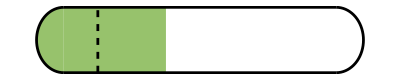

```mathematica
BackGrndBox2=Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.2],
{Rectangle[{xl⟦2⟧,yc⟦2⟧-h},{xnr⟦2⟧,yc⟦2⟧+h}]},
{Disk[{xl⟦2⟧,yc⟦2⟧},h,{π/2,3π/2}]}
}];
OutLineBox2 = Graphics[{
RGBColor["Black"],
Thickness[0.005],
Circle[{xl⟦2⟧,yc⟦2⟧},h,{π/2,3π/2}],
Circle[{xr⟦4⟧,yc⟦2⟧},h,{-π/2,π/2}],
Line[{{xl⟦2⟧,yc⟦2⟧-h},{xr⟦4⟧,yc⟦2⟧-h}}],
Line[{{xl⟦2⟧,yc⟦2⟧+h},{xr⟦4⟧,yc⟦2⟧+h}}]
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Abreak2=Graphics[{
RGBColor["Black"],
Dashed,
Thickness[0.005],{
Line[{{xr⟦1⟧,yc⟦2⟧-h},{xr⟦1⟧,yc⟦2⟧+h}}]}
}];
Show[BackGrndBox2,OutLineBox2,Abreak2]
(*Export["ETHPill2.pdf",%,Rasterize-> False]*)
```

```mathematica
"ETHPill2.pdf"
```

ETHPill2.pdf

```mathematica
"ETHPill2.pdf"
```

ETHPill2.pdf

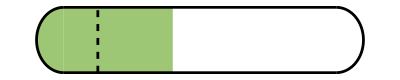

```mathematica
BackGrndBox3=Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.25],
{Rectangle[{xl⟦3⟧,yc⟦3⟧-h},{xnr⟦3⟧,yc⟦3⟧+h}]},
{Disk[{xl⟦3⟧,yc⟦3⟧},h,{π/2,3π/2}]}
}];
OutLineBox3 = Graphics[{
RGBColor["Black"],
Thickness[0.005],
Circle[{xl⟦3⟧,yc⟦3⟧},h,{π/2,3π/2}],
Circle[{xr⟦4⟧,yc⟦3⟧},h,{-π/2,π/2}],
Line[{{xl⟦3⟧,yc⟦3⟧-h},{xr⟦4⟧,yc⟦3⟧-h}}],
Line[{{xl⟦3⟧,yc⟦3⟧+h},{xr⟦4⟧,yc⟦3⟧+h}}]
}];
Abreak3=Graphics[{
RGBColor["Black"],
Dashed,
Thickness[0.005],{
Line[{{xr⟦1⟧,yc⟦3⟧-h},{xr⟦1⟧,yc⟦3⟧+h}}]}
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[BackGrndBox3,OutLineBox3,Abreak3]
(*Export["ETHPill3.pdf",%,Rasterize-> False]*)
```

```mathematica
"ETHPill3.pdf"
```

ETHPill3.pdf

```mathematica
"ETHPill3.pdf"
```

ETHPill3.pdf

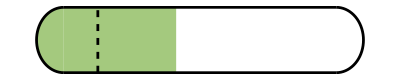

```mathematica
BackGrndBox4=Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.3],
{Rectangle[{xl⟦4⟧,yc⟦4⟧-h},{xnr⟦4⟧,yc⟦4⟧+h}]},
{Disk[{xl⟦4⟧,yc⟦4⟧},h,{π/2,3π/2}]}
}];
OutLineBox4= Graphics[{
RGBColor["Black"],
Thickness[0.005],
Circle[{xl⟦4⟧,yc⟦4⟧},h,{π/2,3π/2}],
Circle[{xr⟦4⟧,yc⟦4⟧},h,{-π/2,π/2}],
Line[{{xl⟦4⟧,yc⟦4⟧-h},{xr⟦4⟧,yc⟦4⟧-h}}],
Line[{{xl⟦4⟧,yc⟦4⟧+h},{xr⟦4⟧,yc⟦4⟧+h}}]
}];
Abreak4=Graphics[{
RGBColor["Black"],
Dashed,
Thickness[0.005],{
Line[{{xr⟦1⟧,yc⟦4⟧-h},{xr⟦1⟧,yc⟦4⟧+h}}]}
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[BackGrndBox4,OutLineBox4,Abreak4]
(*Export["ETHPill4.pdf",%,Rasterize-> False]*)
```

```mathematica
"ETHPill4.pdf"
```

ETHPill4.pdf

```mathematica
"ETHPill4.pdf"
```

ETHPill4.pdf

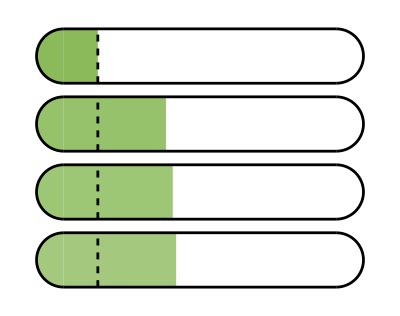

```mathematica
Show[
BackGrndBox1,OutLineBox1,Abreak1,
BackGrndBox2,OutLineBox2,Abreak2,
BackGrndBox3,OutLineBox3,Abreak3,
BackGrndBox4,OutLineBox4,Abreak4]
(*Export["ETHPillNP.pdf",%,Rasterize-> False]*)
```

```mathematica
"ETHPillNP.pdf"
```

ETHPillNP.pdf

```mathematica
"ETHPillNP.pdf"
```

ETHPillNP.pdf

## Adding Correlations

```mathematica
xlf={-2,-2,-2,-2};
xrf={-1.5,-0.5,0.5,2};
ycf={0,-1,-2,-3};
hf=0.3;
```

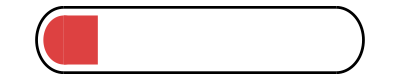

```mathematica
BackGrndBox1F=Graphics[{
Blend[{SpikeBallRed,RGBColor["White"]},0.1],
{Rectangle[{xlf⟦1⟧,ycf⟦1⟧-hf},{xrf⟦1⟧,ycf⟦1⟧+hf}]},
{Disk[{xlf⟦1⟧,ycf⟦1⟧},hf,{π/2,3π/2}]},
{Disk[{xlf⟦1⟧,ycf⟦1⟧},hf,{-π/2,π/2}]}
}];
OutLineBox1F = Graphics[{
RGBColor["Black"],
Thickness[0.005],{
Circle[{xl⟦1⟧,yc⟦1⟧},h,{π/2,3π/2}],
Circle[{xr⟦4⟧,yc⟦1⟧},h,{-π/2,π/2}],
Line[{{xl⟦1⟧,yc⟦1⟧-h},{xr⟦4⟧,yc⟦1⟧-h}}],
Line[{{xl⟦1⟧,yc⟦1⟧+h},{xr⟦4⟧,yc⟦1⟧+h}}]}
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[BackGrndBox1F,OutLineBox1F]
(*Export["ETHPill1F.pdf",%,Rasterize-> False]*)
```

```mathematica
"ETHPill1F.pdf"
```

ETHPill1F.pdf

```mathematica
"ETHPill1F.pdf"
```

ETHPill1F.pdf

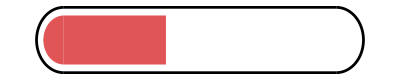

```mathematica
BackGrndBox2F=Graphics[{
Blend[{SpikeBallRed,RGBColor["White"]},0.2],
{Rectangle[{xlf⟦2⟧,ycf⟦2⟧-hf},{xrf⟦2⟧,ycf⟦2⟧+hf}]},
{Disk[{xlf⟦2⟧,ycf⟦2⟧},hf,{π/2,3π/2}]}
}];
OutLineBox2F= Graphics[{
RGBColor["Black"],
Thickness[0.005],
Circle[{xl⟦2⟧,yc⟦2⟧},h,{π/2,3π/2}],
Circle[{xr⟦4⟧,yc⟦2⟧},h,{-π/2,π/2}],
Line[{{xl⟦2⟧,yc⟦2⟧-h},{xr⟦4⟧,yc⟦2⟧-h}}],
Line[{{xl⟦2⟧,yc⟦2⟧+h},{xr⟦4⟧,yc⟦2⟧+h}}]
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[BackGrndBox2F,OutLineBox2F]
(*Export["ETHPill2F.pdf",%,Rasterize-> False]*)
```

```mathematica
"ETHPill2F.pdf"
```

ETHPill2F.pdf

```mathematica
"ETHPill2F.pdf"
```

ETHPill2F.pdf

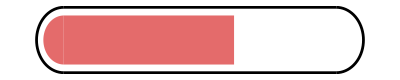

```mathematica
BackGrndBox3F=Graphics[{
Blend[{SpikeBallRed,RGBColor["White"]},0.3],
{Rectangle[{xlf⟦3⟧,ycf⟦3⟧-hf},{xrf⟦3⟧,ycf⟦3⟧+hf}]},
{Disk[{xlf⟦3⟧,ycf⟦3⟧},hf,{π/2,3π/2}]}
}];
OutLineBox3F = Graphics[{
RGBColor["Black"],
Thickness[0.005],
Circle[{xl⟦3⟧,yc⟦3⟧},h,{π/2,3π/2}],
Circle[{xr⟦4⟧,yc⟦3⟧},h,{-π/2,π/2}],
Line[{{xl⟦3⟧,yc⟦3⟧-h},{xr⟦4⟧,yc⟦3⟧-h}}],
Line[{{xl⟦3⟧,yc⟦3⟧+h},{xr⟦4⟧,yc⟦3⟧+h}}]
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[BackGrndBox3F,OutLineBox3F]
(*Export["ETHPill3F.pdf",%,Rasterize-> False]*)
```

```mathematica
"ETHPill3F.pdf"
```

ETHPill3F.pdf

```mathematica
"ETHPill3F.pdf"
```

ETHPill3F.pdf

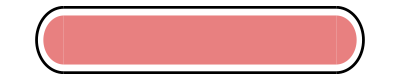

```mathematica
BackGrndBox4F=Graphics[{
Blend[{SpikeBallRed,RGBColor["White"]},0.4],
{Rectangle[{xlf⟦4⟧,ycf⟦4⟧-hf},{xrf⟦4⟧,ycf⟦4⟧+hf}]},
{Disk[{xlf⟦4⟧,ycf⟦4⟧},hf,{π/2,3π/2}]},
{Disk[{xrf⟦4⟧,ycf⟦4⟧},hf,{-π/2,π/2}]}
}];
OutLineBox4F= Graphics[{
RGBColor["Black"],
Thickness[0.005],
Circle[{xl⟦4⟧,yc⟦4⟧},h,{π/2,3π/2}],
Circle[{xr⟦4⟧,yc⟦4⟧},h,{-π/2,π/2}],
Line[{{xl⟦4⟧,yc⟦4⟧-h},{xr⟦4⟧,yc⟦4⟧-h}}],
Line[{{xl⟦4⟧,yc⟦4⟧+h},{xr⟦4⟧,yc⟦4⟧+h}}]
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[BackGrndBox4F,OutLineBox4]
(*Export["ETHPill4F.pdf",%,Rasterize-> False]*)
```

```mathematica
"ETHPill4F.pdf"
```

ETHPill4F.pdf

```mathematica
"ETHPill4F.pdf"
```

ETHPill4F.pdf

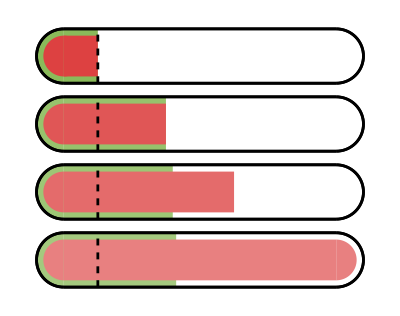

```mathematica
Show[
BackGrndBox1,OutLineBox1,
BackGrndBox2,OutLineBox2,
BackGrndBox3,OutLineBox3,
BackGrndBox4,OutLineBox4,
BackGrndBox1F,OutLineBox1F,
BackGrndBox2F,OutLineBox2F,
BackGrndBox3F,OutLineBox3F,
BackGrndBox4F,OutLineBox4F,
Abreak1,Abreak2,Abreak3,Abreak4]
(*Export["ETHPillNPF.pdf",%,ImageResolution-> 2000,Rasterize-> False]*)
```

```mathematica
"ETHPillNPF.pdf"
```

ETHPillNPF.pdf

```mathematica
"ETHPillNPF.pdf"
```

ETHPillNPF.pdf

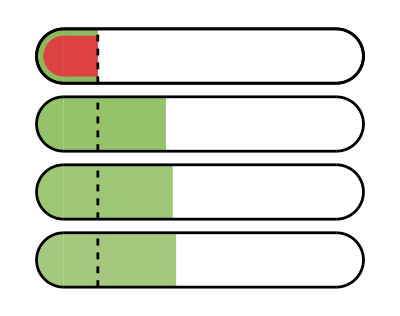

```mathematica
Show[
BackGrndBox1,OutLineBox1,
BackGrndBox2,OutLineBox2,
BackGrndBox3,OutLineBox3,
BackGrndBox4,OutLineBox4,
BackGrndBox1F,OutLineBox1F,
Abreak1,Abreak2,Abreak3,Abreak4]
(*Export["ETHPillNPF1.pdf",%,ImageResolution-> 2000,Rasterize-> False]*)
```

```mathematica
"ETHPillNPF1.pdf"
```

ETHPillNPF1.pdf

```mathematica
"ETHPillNPF1.pdf"
```

ETHPillNPF1.pdf

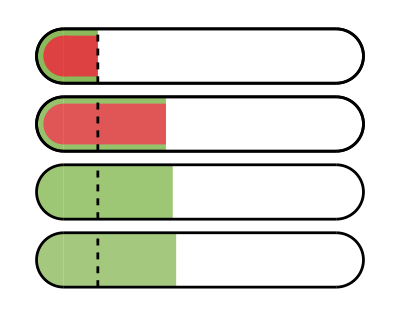

```mathematica
Show[
BackGrndBox1,OutLineBox1,
BackGrndBox2,OutLineBox2,
BackGrndBox3,OutLineBox3,
BackGrndBox4,OutLineBox4,
BackGrndBox1F,OutLineBox1F,
BackGrndBox2F,OutLineBox2F,
Abreak1,Abreak2,Abreak3,Abreak4]
(*Export["ETHPillNPF2.pdf",%,ImageResolution-> 2000,Rasterize-> False]*)
```

```mathematica
"ETHPillNP2.pdf"
```

ETHPillNP2.pdf

```mathematica
"ETHPillNP2.pdf"
```

ETHPillNP2.pdf

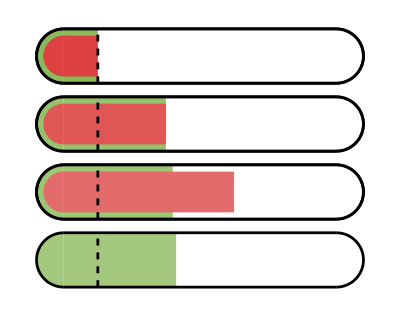

```mathematica
Show[
BackGrndBox1,OutLineBox1,
BackGrndBox2,OutLineBox2,
BackGrndBox3,OutLineBox3,
BackGrndBox4,OutLineBox4,
BackGrndBox1F,OutLineBox1F,
BackGrndBox2F,OutLineBox2F,
BackGrndBox3F,OutLineBox3F,
Abreak1,Abreak2,Abreak3,Abreak4]
(*Export["ETHPillNPF3.pdf",%,ImageResolution-> 2000,Rasterize-> False]*)
```

```mathematica
"ETHPillNPF.pdf"
```

ETHPillNPF.pdf

```mathematica
"ETHPillNPF.pdf"
```

ETHPillNPF.pdf

```mathematica
Show[
BackGrndBox1,OutLineBox1,
BackGrndBox2,OutLineBox2,
BackGrndBox3,OutLineBox3,
BackGrndBox4,OutLineBox4,
BackGrndBox1F,OutLineBox1F,
BackGrndBox2F,OutLineBox2F,
BackGrndBox3F,OutLineBox3F,
BackGrndBox4F,OutLineBox4F,
Abreak1,Abreak2,Abreak3,Abreak4]
(*Export["ETHPillNPF4.pdf",%,ImageResolution-> 2000,Rasterize-> False]*)
```

-Graphics-

```mathematica
"ETHPillNPF.pdf"
```

ETHPillNPF.pdf

```mathematica
"ETHPillNPF.pdf"
```

ETHPillNPF.pdf

## Now MBL Combo Figs

### MBL 1

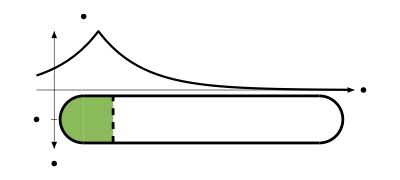

MBLPill_Combo1.pdf

```mathematica
EXPPlotI=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,xr⟦4⟧+0.5},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];

GraphAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦1⟧+1.5}}],
Arrow[{{xl⟦1⟧-0.8,yc⟦1⟧+0.5},{xr⟦4⟧+0.6,yc⟦1⟧+0.5}}]
}
];
TAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Line[{{xl⟦1⟧-0.5-tx,yc⟦1⟧},{xl⟦1⟧-0.5+tx,yc⟦1⟧}}],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦1⟧-0.5}}]
}
];

labels=Graphics[{
Inset[MaTeX["|\\Psi(x)|^2 \\sim e^{-|x|/\\xi}",Magnification->1.5],{xl⟦1⟧,1.75}],
Inset[MaTeX["x",Magnification->1.5],{xr⟦4⟧+1.15-0.4,yc⟦1⟧+0.5}],
Inset[MaTeX["t",Magnification->1.5],{xl⟦1⟧-0.5,yc⟦1⟧-0.75}],
Inset[MaTeX["0",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦1⟧}]
}];

Show[
GraphAxes,TAxes,
BackGrndBox1,OutLineBox1,Abreak1,
EXPPlotI,
labels
]
Export["MBLPill_Combo1.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
"MBLPill_Combo1.pdf"
```

MBLPill_Combo1.pdf

### ETH 2

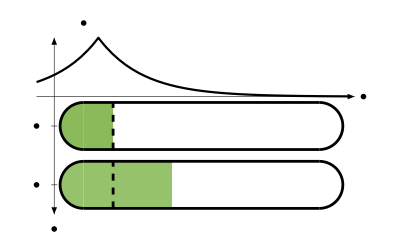

MBLPill_Combo2.pdf

```mathematica
EXPPlot=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,xr⟦4⟧+0.5},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];
EXPPlotCBL=Plot[
{Exp[-Abs[x-xr⟦2⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,(xr⟦1⟧+xr⟦2⟧)/2-0.25},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->yc⟦1⟧+0.5,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
EXPPlotCBR=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,(xr⟦1⟧+xr⟦2⟧)/2-0.25,xr⟦4⟧+0.5},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->yc⟦1⟧+0.5,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
GraphAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦1⟧+1.5}}],
Arrow[{{xl⟦1⟧-0.8,yc⟦1⟧+0.5},{xr⟦4⟧+0.6,yc⟦1⟧+0.5}}]
}
];
TAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Line[{{xl⟦1⟧-0.5-tx,yc⟦1⟧},{xl⟦1⟧-0.5+tx,yc⟦1⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦2⟧},{xl⟦1⟧-0.5+tx,yc⟦2⟧}}],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦2⟧-0.5}}]
}
];

labels=Graphics[{
Inset[MaTeX["|\\Psi(x)|^2 \\sim e^{-|x|/\\xi}",Magnification->1.5],{xl⟦1⟧,1.75}],
Inset[MaTeX["x",Magnification->1.5],{xr⟦4⟧+1.15-0.4,yc⟦1⟧+0.5}],
Inset[MaTeX["t",Magnification->1.5],{xl⟦1⟧-0.5,yc⟦2⟧-0.75}],
Inset[MaTeX["0",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦1⟧}],
Inset[MaTeX["10^{1}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦2⟧}]
}];

PsiGreen = Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.2],
Rectangle[{xl⟦1⟧-0.4,yc⟦1⟧+0.5},{xr⟦2⟧,yc⟦1⟧+1}]
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[
GraphAxes,TAxes,
BackGrndBox1,OutLineBox1,Abreak1,
BackGrndBox2,OutLineBox2,Abreak2,
EXPPlot,
labels
]

Export["MBLPill_Combo2.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
"MBLPill_Combo2.pdf"
```

MBLPill_Combo2.pdf

### ETH 3

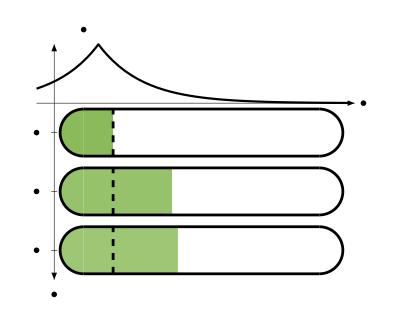

MBLPill_Combo3.pdf

```mathematica
EXPPlot=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,xr⟦4⟧+0.5},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];

GraphAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦1⟧+1.5}}],
Arrow[{{xl⟦1⟧-0.8,yc⟦1⟧+0.5},{xr⟦4⟧+0.6,yc⟦1⟧+0.5}}]
}
];
TAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Line[{{xl⟦1⟧-0.5-tx,yc⟦1⟧},{xl⟦1⟧-0.5+tx,yc⟦1⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦2⟧},{xl⟦1⟧-0.5+tx,yc⟦2⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦3⟧},{xl⟦1⟧-0.5+tx,yc⟦3⟧}}],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦3⟧-0.5}}]
}
];

labels=Graphics[{
Inset[MaTeX["|\\Psi(x)|^2 \\sim e^{-|x|/\\xi}",Magnification->1.5],{xl⟦1⟧,1.75}],
Inset[MaTeX["x",Magnification->1.5],{xr⟦4⟧+1.15-0.4,yc⟦1⟧+0.5}],
Inset[MaTeX["t",Magnification->1.5],{xl⟦1⟧-0.5,yc⟦3⟧-0.75}],
Inset[MaTeX["0",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦1⟧}],
Inset[MaTeX["10^{1}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦2⟧}],
Inset[MaTeX["10^{2}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦3⟧}]
}];

PsiGreen = Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.4],
Rectangle[{xl⟦1⟧-0.4,yc⟦1⟧+0.5},{xr⟦3⟧,yc⟦1⟧+1}]
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[
GraphAxes,TAxes,EXPPlot,
BackGrndBox1,OutLineBox1,Abreak1,
BackGrndBox2,OutLineBox2,Abreak2,
BackGrndBox3,OutLineBox3,Abreak3,
labels
]
Export["MBLPill_Combo3.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
"MBLPill_Combo3.pdf"
```

MBLPill_Combo3.pdf

### ETH 4

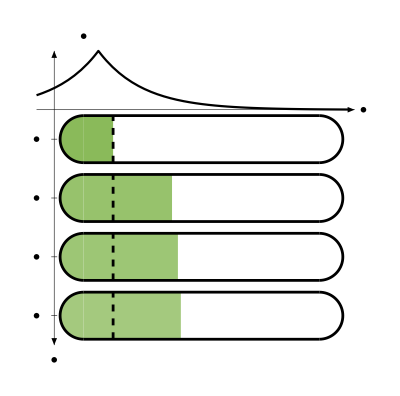

ETHPill_Combo4.pdf

```mathematica
EXPPlot=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,xr⟦4⟧+0.5},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];
GraphAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦1⟧+1.5}}],
Arrow[{{xl⟦1⟧-0.8,yc⟦1⟧+0.5},{xr⟦4⟧+0.6,yc⟦1⟧+0.5}}]
}
];
TAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Line[{{xl⟦1⟧-0.5-tx,yc⟦1⟧},{xl⟦1⟧-0.5+tx,yc⟦1⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦2⟧},{xl⟦1⟧-0.5+tx,yc⟦2⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦3⟧},{xl⟦1⟧-0.5+tx,yc⟦3⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦4⟧},{xl⟦1⟧-0.5+tx,yc⟦4⟧}}],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦4⟧-0.5}}]
}
];

labels=Graphics[{
Inset[MaTeX["|\\Psi(x)|^2 \\sim e^{-|x|/\\xi}",Magnification->1.5],{xl⟦1⟧,1.75}],
Inset[MaTeX["x",Magnification->1.5],{xr⟦4⟧+1.15-0.4,yc⟦1⟧+0.5}],
Inset[MaTeX["t",Magnification->1.5],{xl⟦1⟧-0.5,yc⟦4⟧-0.75}],
Inset[MaTeX["0",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦1⟧}],
Inset[MaTeX["10^{1}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦2⟧}],
Inset[MaTeX["10^{2}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦3⟧}],
Inset[MaTeX["10^{3}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦4⟧}]
}];

PsiGreen = Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.6],
Rectangle[{xl⟦1⟧-0.4,yc⟦1⟧+0.5},{xr⟦4⟧+0.4,yc⟦1⟧+1}]
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[
GraphAxes,TAxes,EXPPlot,
BackGrndBox1,OutLineBox1,Abreak1,
BackGrndBox2,OutLineBox2,Abreak2,
BackGrndBox3,OutLineBox3,Abreak3,
BackGrndBox4,OutLineBox4,Abreak4,
labels
]
Export["ETHPill_Combo4.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
"ETHPill_Combo4.pdf"
```

ETHPill_Combo4.pdf

### ETH 4 + 1 C

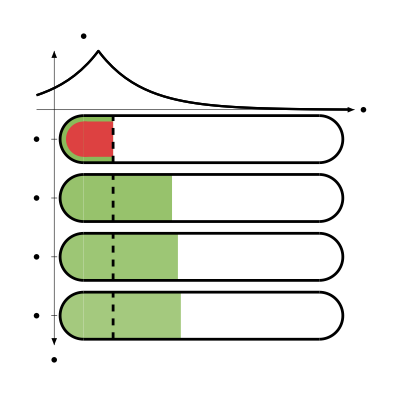

MBLPill_Combo1_F1.pdf

```mathematica
EXPPlot=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5,
Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,xr⟦4⟧+0.5},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];
GraphAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦1⟧+1.5}}],
Arrow[{{xl⟦1⟧-0.8,yc⟦1⟧+0.5},{xr⟦4⟧+0.6,yc⟦1⟧+0.5}}]
}
];
TAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Line[{{xl⟦1⟧-0.5-tx,yc⟦1⟧},{xl⟦1⟧-0.5+tx,yc⟦1⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦2⟧},{xl⟦1⟧-0.5+tx,yc⟦2⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦3⟧},{xl⟦1⟧-0.5+tx,yc⟦3⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦4⟧},{xl⟦1⟧-0.5+tx,yc⟦4⟧}}],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦4⟧-0.5}}]
}
];

labels=Graphics[{
Inset[MaTeX["|\\Psi(x)|^2 \\sim e^{-|x|/\\xi}",Magnification->1.5],{xl⟦1⟧,1.75}],
Inset[MaTeX["x",Magnification->1.5],{xr⟦4⟧+1.15-0.4,yc⟦1⟧+0.5}],
Inset[MaTeX["t",Magnification->1.5],{xl⟦1⟧-0.5,yc⟦4⟧-0.75}],
Inset[MaTeX["0",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦1⟧}],
Inset[MaTeX["10^{1}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦2⟧}],
Inset[MaTeX["10^{2}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦3⟧}],
Inset[MaTeX["10^{3}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦4⟧}]
}];

PsiGreen = Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.1],
Rectangle[{xl⟦1⟧-0.4,yc⟦1⟧+0.5},{xr⟦1⟧,yc⟦1⟧+1}]
}];
(*{Disk[{1.75,0},0.4,{-π/2,π/2}]}*)
Show[
GraphAxes,TAxes,EXPPlot,
BackGrndBox1,BackGrndBox1F,OutLineBox1,Abreak1,
BackGrndBox2,OutLineBox2,Abreak2,
BackGrndBox3,OutLineBox3,Abreak3,
BackGrndBox4,OutLineBox4,Abreak4,
labels
]
Export["MBLPill_Combo1_F1.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
"MBLPill_Combo1_F1.pdf"
```

MBLPill_Combo1_F1.pdf

### ETH 4 + 2 C

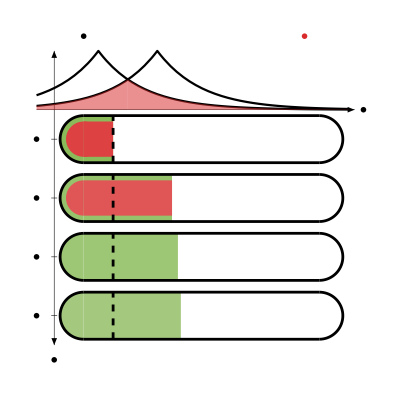
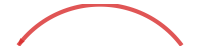

MBLPill_Combo2_F2.pdf

```mathematica
EXPPlot=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5,
Exp[-Abs[x-xr⟦2⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,xr⟦4⟧+0.5},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];
EXPPlotCBL=Plot[
{Exp[-Abs[x-xr⟦2⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,(xr⟦1⟧+xr⟦2⟧)/2-0.25},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->yc⟦1⟧+0.5,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
EXPPlotCBR=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,(xr⟦1⟧+xr⟦2⟧)/2-0.25,xr⟦4⟧+0.5},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->yc⟦1⟧+0.5,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
GraphAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦1⟧+1.5}}],
Arrow[{{xl⟦1⟧-0.8,yc⟦1⟧+0.5},{xr⟦4⟧+0.6,yc⟦1⟧+0.5}}]
}
];
TAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Line[{{xl⟦1⟧-0.5-tx,yc⟦1⟧},{xl⟦1⟧-0.5+tx,yc⟦1⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦2⟧},{xl⟦1⟧-0.5+tx,yc⟦2⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦3⟧},{xl⟦1⟧-0.5+tx,yc⟦3⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦4⟧},{xl⟦1⟧-0.5+tx,yc⟦4⟧}}],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦4⟧-0.5}}]
}
];

labels=Graphics[{
Inset[MaTeX["|\\Psi(x)|^2 \\sim e^{-|x|/\\xi}",Magnification->1.5],{xl⟦1⟧,1.75}],
Inset[MaTeX["x",Magnification->1.5],{xr⟦4⟧+1.15-0.4,yc⟦1⟧+0.5}],
Inset[MaTeX["t",Magnification->1.5],{xl⟦1⟧-0.5,yc⟦4⟧-0.75}],
Inset[MaTeX["0",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦1⟧}],
Inset[MaTeX["10^{1}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦2⟧}],
Inset[MaTeX["10^{2}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦3⟧}],
Inset[MaTeX["10^{3}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦4⟧}]
}];

labelsUeff=Graphics[{SpikeBallRed,
Inset[MaTeX["\\color{spikeballred} U_{eff}\\sim U_o e^{-|x_i - x_j|/\\xi}",
Magnification->1.5],{(xr⟦2⟧)/2+2,1.75}]
}];


ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[SpikeBallRed,Opacity[0.8],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]


rdsAndAngls={{0.075,{0.2π,π 0.8}}};
UArc = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{(xr⟦1⟧+xr⟦2⟧)/2-0.25,yc⟦1⟧+0.5+1}]
}];



Show[
GraphAxes,TAxes,EXPPlot,EXPPlotCBL,EXPPlotCBR,
BackGrndBox1,BackGrndBox1F,OutLineBox1,Abreak1,
BackGrndBox2,BackGrndBox2F,OutLineBox2,Abreak2,
BackGrndBox3,OutLineBox3,Abreak3,
BackGrndBox4,OutLineBox4,Abreak4,
labels,UArc ,labelsUeff
]

Export["MBLPill_Combo2_F2.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
"MBLPill_Combo2_F2.pdf"
```

MBLPill_Combo2_F2.pdf

```mathematica
SpikeBallRed

Hue[0,0.8,0.85]
ColorData[93,"ColorList"]⟦1⟧
```

Hue[0, 0.8, 0.85]

Hue[0, 0.8, 0.85]

Hue[0, 0.8, 0.85]

^3

### ETH 4 + 3 C

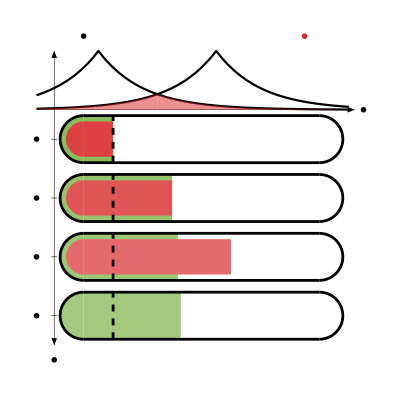
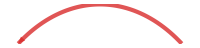

MBLPill_Combo3_F3.pdf

```mathematica
EXPPlot=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5,
Exp[-Abs[x-xr⟦3⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,xr⟦4⟧+0.5},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];
EXPPlotCBL=Plot[
{Exp[-Abs[x-xr⟦3⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,(xr⟦1⟧+xr⟦3⟧)/2-0.25},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->yc⟦1⟧+0.5,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
EXPPlotCBR=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,(xr⟦1⟧+xr⟦3⟧)/2-0.25,xr⟦4⟧+0.5},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->yc⟦1⟧+0.5,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
GraphAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦1⟧+1.5}}],
Arrow[{{xl⟦1⟧-0.8,yc⟦1⟧+0.5},{xr⟦4⟧+0.6,yc⟦1⟧+0.5}}]
}
];
TAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Line[{{xl⟦1⟧-0.5-tx,yc⟦1⟧},{xl⟦1⟧-0.5+tx,yc⟦1⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦2⟧},{xl⟦1⟧-0.5+tx,yc⟦2⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦3⟧},{xl⟦1⟧-0.5+tx,yc⟦3⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦4⟧},{xl⟦1⟧-0.5+tx,yc⟦4⟧}}],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦4⟧-0.5}}]
}
];
labels=Graphics[{
Inset[MaTeX["|\\Psi(x)|^2 \\sim e^{-|x|/\\xi}",Magnification->1.5],{xl⟦1⟧,1.75}],
Inset[MaTeX["x",Magnification->1.5],{xr⟦4⟧+1.15-0.4,yc⟦1⟧+0.5}],
Inset[MaTeX["t",Magnification->1.5],{xl⟦1⟧-0.5,yc⟦4⟧-0.75}],
Inset[MaTeX["0",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦1⟧}],
Inset[MaTeX["10^{1}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦2⟧}],
Inset[MaTeX["10^{2}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦3⟧}],
Inset[MaTeX["10^{3}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦4⟧}]
}];

PsiGreen = Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.4],
Rectangle[{xl⟦1⟧-0.4,yc⟦1⟧+0.5},{xr⟦3⟧,yc⟦1⟧+1}]
}];


ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[SpikeBallRed,Opacity[0.8],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]


rdsAndAngls={{0.305,{0.3π,π 0.7}}};
UArc = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{(xr⟦1⟧+xr⟦3⟧)/2-0.25,yc⟦1⟧+0.5+1}]
}];


labelsUeff=Graphics[{SpikeBallRed,
Inset[MaTeX["\\color{spikeballred} U_{eff}\\sim U_o e^{-|x_i - x_j|/\\xi}",
Magnification->1.5],{(xr⟦2⟧)/2+2,1.75}]
}];


Show[
GraphAxes,TAxes,EXPPlot,EXPPlotCBL,EXPPlotCBR,
BackGrndBox1,BackGrndBox1F,OutLineBox1,Abreak1,
BackGrndBox2,BackGrndBox2F,OutLineBox2,Abreak2,
BackGrndBox3,BackGrndBox3F,OutLineBox3,Abreak3,
BackGrndBox4,OutLineBox4,Abreak4,
labels,UArc ,labelsUeff
]
Export["MBLPill_Combo3_F3.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
"MBLPill_Combo3_F3.pdf"
```

MBLPill_Combo3_F3.pdf

### ETH 4 + 4 C

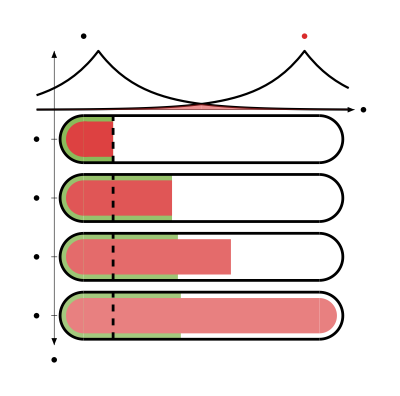
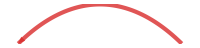

MBLPill_Combo4_F4.pdf

```mathematica
EXPPlot=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5,
Exp[-Abs[x-xr⟦4⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,xr⟦4⟧+0.5},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];
EXPPlotCBL=Plot[
{Exp[-Abs[x-xr⟦4⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,(xr⟦1⟧+xr⟦4⟧)/2-0.25},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->yc⟦1⟧+0.5,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
EXPPlotCBR=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,(xr⟦1⟧+xr⟦4⟧)/2-0.25,xr⟦4⟧+0.5},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->yc⟦1⟧+0.5,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
GraphAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦1⟧+1.5}}],
Arrow[{{xl⟦1⟧-0.8,yc⟦1⟧+0.5},{xr⟦4⟧+0.6,yc⟦1⟧+0.5}}]
}
];
TAxes=Graphics[
{RGBColor["Black"],Thickness[0.001],
Line[{{xl⟦1⟧-0.5-tx,yc⟦1⟧},{xl⟦1⟧-0.5+tx,yc⟦1⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦2⟧},{xl⟦1⟧-0.5+tx,yc⟦2⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦3⟧},{xl⟦1⟧-0.5+tx,yc⟦3⟧}}],
Line[{{xl⟦1⟧-0.5-tx,yc⟦4⟧},{xl⟦1⟧-0.5+tx,yc⟦4⟧}}],
Arrow[{{xl⟦1⟧-0.5,yc⟦1⟧+0.5},{xl⟦1⟧-0.5,yc⟦4⟧-0.5}}]
}
];
labels=Graphics[{
Inset[MaTeX["|\\Psi(x)|^2 \\sim e^{-|x|/\\xi}",Magnification->1.5],{xl⟦1⟧,1.75}],
Inset[MaTeX["x",Magnification->1.5],{xr⟦4⟧+1.15-0.4,yc⟦1⟧+0.5}],
Inset[MaTeX["t",Magnification->1.5],{xl⟦1⟧-0.5,yc⟦4⟧-0.75}],
Inset[MaTeX["0",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦1⟧}],
Inset[MaTeX["10^{1}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦2⟧}],
Inset[MaTeX["10^{2}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦3⟧}],
Inset[MaTeX["10^{3}",Magnification->1.5],{xl⟦1⟧-0.8,yc⟦4⟧}]
}];
PsiGreen = Graphics[{
Blend[{atomgreen,RGBColor["White"]},0.4],
Rectangle[{xl⟦1⟧-0.4,yc⟦1⟧+0.5},{xr⟦4⟧+0.4,yc⟦1⟧+1}]
}];


ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[SpikeBallRed,Opacity[0.8],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]


rdsAndAngls={{7,{0.4π,π 0.6}}};
UArc = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{(xr⟦1⟧+xr⟦4⟧)/2-0.25,yc⟦1⟧+0.5+1}]
}];


labelsUeff=Graphics[{SpikeBallRed,
Inset[MaTeX["\\color{spikeballred} U_{eff}\\sim U_o e^{-|x_i - x_j|/\\xi}",
Magnification->1.5],{(xr⟦2⟧)/2+2,1.75}]
}];


Show[
GraphAxes,TAxes,EXPPlot,EXPPlotCBL,EXPPlotCBR,
BackGrndBox1,BackGrndBox1F,OutLineBox1,Abreak1,
BackGrndBox2,BackGrndBox2F,OutLineBox2,Abreak2,
BackGrndBox3,BackGrndBox3F,OutLineBox3,Abreak3,
BackGrndBox4,BackGrndBox4F,OutLineBox4,Abreak4,
labels,UArc ,labelsUeff
]
Export["MBLPill_Combo4_F4.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
"MBLPill_Combo4_F4.pdf"
```

MBLPill_Combo4_F4.pdf

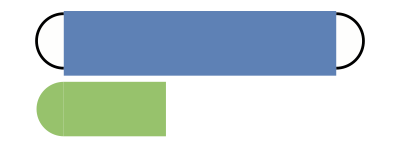

```mathematica
BackGrndBox1=Graphics[
{Blend[{atomgreen,RGBColor["White"]},0.99],
Rectangle[{xl⟦4⟧,yc⟦1⟧-h},{xr⟦4⟧,yc⟦1⟧+h}],
Disk[{xl⟦4⟧,yc⟦1⟧},h,{π/2,3π/2}],
Disk[{xr⟦4⟧,yc⟦1⟧},h,{-π/2,π/2}]}
];
EXPPlot=Plot[
{Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5,
Exp[-Abs[x-xr⟦1⟧+0.25]/0.75]+yc⟦1⟧+0.5},
{x,xl⟦1⟧-0.8,xr⟦4⟧+0.5},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];
BoxPlot=Plot[yc⟦1⟧,
{x,xl⟦1⟧,xr⟦4⟧},
Axes-> False,
PlotStyle->{Thickness[0.8]}
];
Show[
BackGrndBox1,BackGrndBox2,OutLineBox1,Abreak1,BoxPlot
]
```

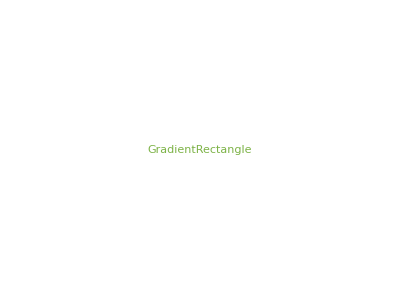

```mathematica
Graphics[{atomgreen,ChartElementData["GradientRectangle",,"GradientOrigin"->Left][{{0,1},{0,1}}]}]
```